```mathematica
<<FeynCalc`
```

FeynCalc 10.0.0 (dev version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

```mathematica
ubar2=SpinorUBar[p2,m2];
u1=SpinorU[p1,m1];
```

```mathematica
ubar2
```

SpinorUBar[p2,m2]

```mathematica
Vwt=ubar2.GS[q1+q2].u1
```

SpinorUBar[p2,m2].GS[q1+q2].SpinorU[p1,m1]

```mathematica
DiracSimplify[Vwt]
```

(φ(OverBar[p2],m2)).(γ̄·OverBar[q1]+γ̄·OverBar[q2]).(φ(OverBar[p1],m1))

```mathematica
PauliSigma
```

```mathematica
(*PauliXi[I] represents a two-component Pauli spinor ξ, while PauliXi[-I] stands for ξ^ᵀ*)
```

```mathematica
PauliXi[I].PauliXi[-I]
```

ξ.ξ^†

```mathematica
PauliSimplify[PauliXi[-I].PauliXi[I]]
```

ξ^†.ξ

```mathematica
PauliXi[-I].SIS[p].PauliXi[I]//PauliSigmaExpand
```

ξ^†.(σ̄·p̄).ξ

```mathematica
PauliChainCombine[PauliXi[-I].PauliXi[I]]
```

ξ^†.ξ

```mathematica
Integrate[Sin[x]Cos[x],{x,0,π}]
```

0

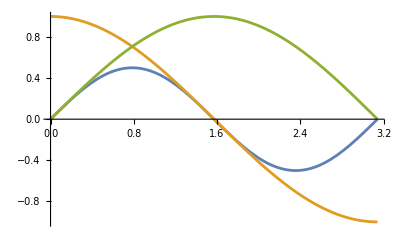

```mathematica
Plot[{Sin[x]Cos[x],Cos[x],Sin[x]},{x,0,π}]
```

```mathematica
LegendreP[0,x]
```

1

```mathematica
GA[].GA[μ]
```

```mathematica
PauliSigma[x,3]
```

PauliSigma(x)

```mathematica
CSIS[a].CSIS[b]//PauliSigmaS
```

(σ̄·ā).(σ̄·b̄)

```mathematica
CSIS[a,b]
```

(σ̄·ā).(σ̄·b̄)

```mathematica
gamma0={{1,0},{0,-1}};
gammai:={{0,1},{-1,0}};
```

```mathematica
udagger2= {1,CSIS[Subscript[p, 2]]/(Subscript[EE, 2]+Subscript[M, 2])};
u1= {1,CSIS[Subscript[p, 1]]/(Subscript[EE, 1]+Subscript[M, 1])};
```

```mathematica
t1=udagger2.gamma0.gamma0 (Subscript[ω, 1]+Subscript[ω, 2])
```

{ω_1+ω_2,((ω_1+ω_2) σ̄·(p̄)_2)/(EE_2+M_2)}

```mathematica
t11=t1.gammai
```

{-((ω_1+ω_2) σ̄·(p̄)_2)/(EE_2+M_2),ω_1+ω_2}

```mathematica
t2=-udagger2.gamma0.gammai
```

{-(σ̄·(p̄)_2)/(EE_2+M_2),-1}

```mathematica
t22={-CSIS[Subscript[p, 2],Subscript[k, 1]+Subscript[k, 2]]/(Subscript[EE, 2]+Subscript[M, 2]),-CSIS[Subscript[k, 1]+Subscript[k, 2]]}
```

{-((σ̄·(p̄)_2).(σ̄·((k̄)_1+(k̄)_2)))/(EE_2+M_2),-(σ̄·((k̄)_1+(k̄)_2))}

```mathematica
t3=t1+t22//Simplify
```

{-((σ̄·(p̄)_2).(σ̄·((k̄)_1+(k̄)_2)))/(EE_2+M_2)+ω_1+ω_2,((ω_1+ω_2) σ̄·(p̄)_2)/(EE_2+M_2)-σ̄·((k̄)_1+(k̄)_2)}

```mathematica
t3//StandardForm
```

{-(CSIS[p_2].CSIS[k_1+k_2])/(EE_2+M_2)+ω_1+ω_2,-CSIS[k_1+k_2]+(CSIS[p_2] (ω_1+ω_2))/(EE_2+M_2)}

```mathematica
t4=t3[[1]]+(-CSIS[Subscript[k, 1]+Subscript[k, 2],Subscript[p, 1]]+(CSIS[Subscript[p, 2],Subscript[p, 1]] (Subscript[ω, 1]+Subscript[ω, 2]))/(Subscript[EE, 2]+Subscript[M, 2]))/(Subscript[EE, 1]+Subscript[M, 1])/.Subscript[k, 1]+Subscript[k, 2]->-Subscript[p, 1]-Subscript[p, 2]//FullSimplify
```

(((ω_1+ω_2) (σ̄·(p̄)_2).(σ̄·(p̄)_1))/(EE_2+M_2)-(σ̄·(-(p̄)_1-(p̄)_2)).(σ̄·(p̄)_1))/(EE_1+M_1)-((σ̄·(p̄)_2).(σ̄·(-(p̄)_1-(p̄)_2)))/(EE_2+M_2)+ω_1+ω_2

```mathematica
t5=t3[[1]]/.Subscript[k, 1]+Subscript[k, 2]->-Subscript[p, 1]-Subscript[p, 2]//PauliSimplify//FullSimplify
```

((σ̄·(p̄)_2).(σ̄·(p̄)_1)+((p̄)_2)^2+(ω_1+ω_2) (EE_2+M_2))/(EE_2+M_2)

```mathematica
t6=(-CSIS[Subscript[k, 1]+Subscript[k, 2],Subscript[p, 1]]+(CSIS[Subscript[p, 2],Subscript[p, 1]] (Subscript[ω, 1]+Subscript[ω, 2]))/(Subscript[EE, 2]+Subscript[M, 2]))/(Subscript[EE, 1]+Subscript[M, 1])/.Subscript[k, 1]+Subscript[k, 2]->-Subscript[p, 1]-Subscript[p, 2]//PauliSimplify//FullSimplify
```

((EE_2+M_2+ω_1+ω_2) (σ̄·(p̄)_2).(σ̄·(p̄)_1)+((p̄)_1)^2 (EE_2+M_2))/((EE_1+M_1) (EE_2+M_2))

```mathematica
PauliSimplify[t5+t6]//FullSimplify
```

((EE_1+EE_2+M_1+M_2+ω_1+ω_2) (σ̄·(p̄)_2).(σ̄·(p̄)_1)+(EE_2+M_2) (((p̄)_1)^2+(ω_1+ω_2) (EE_1+M_1))+((p̄)_2)^2 (EE_1+M_1))/((EE_1+M_1) (EE_2+M_2))

```mathematica
%/.Subscript[EE, 1]+Subscript[EE, 2]+Subscript[ω, 1]+Subscript[ω, 2]->2Sqrt[s]
```

((EE_2+M_2) (((p̄)_1)^2+(ω_1+ω_2) (EE_1+M_1))+((p̄)_2)^2 (EE_1+M_1)+(M_1+M_2+2 √s) (σ̄·(p̄)_2).(σ̄·(p̄)_1))/((EE_1+M_1) (EE_2+M_2))

```mathematica
%/.Subscript[ω, 1]+Subscript[ω, 2]->2Sqrt[s]-Subscript[EE, 1]-Subscript[EE, 2]
```

((EE_2+M_2) (((p̄)_1)^2+(EE_1+M_1) (-EE_1-EE_2+2 √s))+((p̄)_2)^2 (EE_1+M_1)+(M_1+M_2+2 √s) (σ̄·(p̄)_2).(σ̄·(p̄)_1))/((EE_1+M_1) (EE_2+M_2))

```mathematica
%//StandardForm
```

1/((EE_1+M_1) (EE_2+M_2))(CartesianPair[CartesianMomentum[p_2],CartesianMomentum[p_2]] (EE_1+M_1)+(CartesianPair[CartesianMomentum[p_1],CartesianMomentum[p_1]]+(2 √s-EE_1-EE_2) (EE_1+M_1)) (EE_2+M_2)+PauliSigma[CartesianMomentum[p_2]].PauliSigma[CartesianMomentum[p_1]] (2 √s+M_1+M_2))

```mathematica
%/.CartesianPair[CartesianMomentum[Subscript[p, 1]],CartesianMomentum[Subscript[p, 1]]]->(Subscript[EE, 1]-Subscript[M, 1])(Subscript[EE, 1]+Subscript[M, 1])//Simplify
```

((M_1+M_2+2 √s) (σ̄·(p̄)_2).(σ̄·(p̄)_1)-(EE_1+M_1) (-((p̄)_2)^2-(EE_2+M_2) (-EE_2-M_1+2 √s)))/((EE_1+M_1) (EE_2+M_2))

```mathematica
%/.CartesianPair[CartesianMomentum[Subscript[p, 2]],CartesianMomentum[Subscript[p, 2]]]->(Subscript[EE, 2]-Subscript[M, 2])(Subscript[EE, 2]+Subscript[M, 2])//FullSimplify
```

((M_1+M_2+2 √s) (σ̄·(p̄)_2).(σ̄·(p̄)_1))/((EE_1+M_1) (EE_2+M_2))-M_1-M_2+2 √s

```mathematica
%/.PauliSigma[CartesianMomentum[Subscript[p, 2]]].PauliSigma[CartesianMomentum[Subscript[p, 1]]]->Subscript[p, 1] Subscript[p, 2] Cos[x]+ⅈ Subscript[p, 1] Subscript[p, 2] Sin[x] CSIS[n]
```

((M_1+M_2+2 √s) (p_1 p_2 cos(x)+ⅈ p_1 p_2 sin(x) σ̄·n̄))/((EE_1+M_1) (EE_2+M_2))-M_1-M_2+2 √s

```mathematica
Integrate[%*Sin[x],{x,0,π}]
```

-2 (M_1+M_2-2 √s)+(ⅈ π p_1 p_2 (M_1+M_2+2 √s) σ̄·n̄)/(2 (EE_1+M_1) (EE_2+M_2))

```mathematica
LegendreP[1,Cos[x]]
```

cos(x)

```mathematica
CartesianPair[CartesianMomentum[Subscript[p, 2]],CartesianMomentum[Subscript[p, 2]]]
```

```mathematica
udagger2.gammaS[{Subscript[ω, 1],Subscript[k, 1]},{Subscript[ω, 2],Subscript[k, 2]}].u1
```

(η nor1 σ̄·(p̄)_1 ((nor2 (-ω_1-ω_2) ξ^† σ̄·(p̄)_2)/(M_2+w_2)-nor2 ξ^† (σ̄·(k̄)_1).(σ̄·(k̄)_2)))/(M_1+w_1)+η nor1 ((nor2 ξ^† (σ̄·(k̄)_1).(σ̄·(k̄)_2) σ̄·(p̄)_2)/(M_2+w_2)+nor2 (ω_1+ω_2) ξ^†)

```mathematica
{1,CSIS[c]}.(CSIS[a]{{0,1},{-1,0}}).{1,CSIS[b]}//PauliChainExpand
```

σ̄·ā σ̄·b̄-σ̄·ā σ̄·c̄

```mathematica
1.2
```

1.2

```mathematica
{1}.{2}
```

2

```mathematica
Dot[1,2]
```

1.2

```mathematica
CSIS[p,q,r,s]//StandardForm
```

CSIS[p].CSIS[q].CSIS[r].CSIS[s]

```mathematica
p={PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]}
```

({0,1} | {1,0}
{0,-ⅈ} | {ⅈ,0}
{1,0} | {0,-1})

```mathematica
p//StandardForm
```

{{{0,1},{1,0}},{{0,-ⅈ},{ⅈ,0}},{{1,0},{0,-1}}}

```mathematica
psum=Sum[PauliMatrix[i],{i,1,3}]
```

(1 | 1-ⅈ
1+ⅈ | -1)

```mathematica
pu={1,0};pd={0,1};
```

```mathematica
pu.psum.pu
```

1

```mathematica
pd.psum.pd
```

-1

```mathematica
pu.psum.pd
```

1-ⅈ

```mathematica
pd.psum.pu
```

1+ⅈ

```mathematica
a={a1,a2,a3};
```

```mathematica
pp=a[[1]] p[[1]]+a[[2]]p[[2]]+a[[3]]p[[3]]
```

(a3 | a1-ⅈ a2
a1+ⅈ a2 | -a3)

```mathematica
{1,0}.pp.{1,0}
```

a3

```mathematica
{0,1}.pp.{0,1}
```

-a3

```mathematica
{0,1}.pp.{1,0}
```

a1+ⅈ a2

```mathematica
{1,0}.pp.{0,1}
```

a1-ⅈ a2